```mathematica
FF[n_, k_] := FF[n,k]=
If[ MangoldtLambda[n] == 0, 0, 
If[ MangoldtLambda[ n ]/Log[n] == 1, 1,
N[If[ Mod[N[Log[n]/MangoldtLambda[n]], 2] == 0, (MangoldtLambda[n]/Log[n]) k, Abs[k]MangoldtLambda[n]/Log[n]]]]]
```

```mathematica
FF[8,0]
```

0.

```mathematica
Mod[(N[Log[6]/MangoldtLambda[6]]),2]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity - ComplexInfinity encountered.

Indeterminate

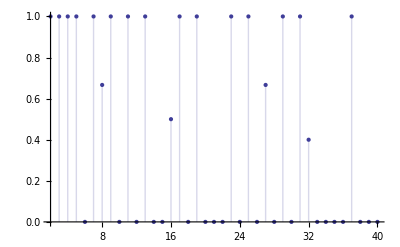

```mathematica
DiscretePlot[ FF[n,2],{n,2,40}]
```

```mathematica
FG[n_, k_, s_ ]:= FG[n,k,s]=Sum[ FF[j,s]( 1/(k!)-FG[Floor[n/j], k+1, s]), {j,2,n}]
```

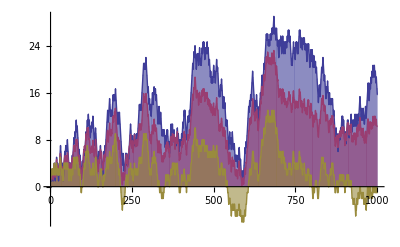

```mathematica
DiscretePlot[ {FG[n,1,-1],FG[n,1,0],FG[n,1,1]},{n,2,1000}, ExtentSize->Full]
```

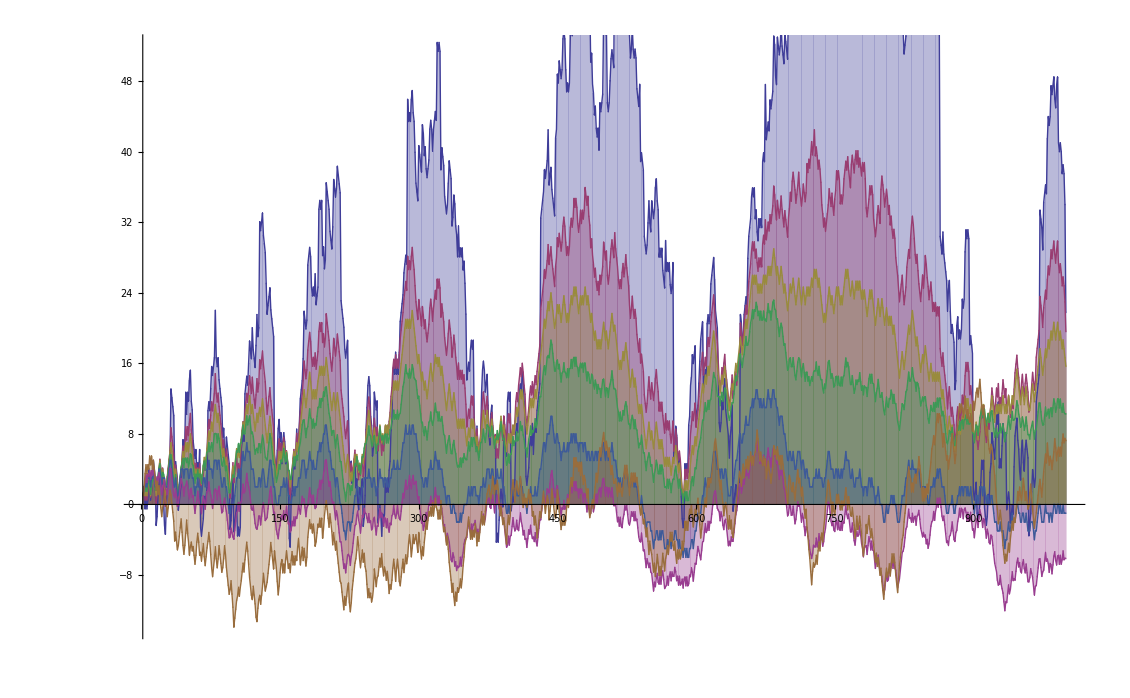

```mathematica
DiscretePlot[ {FG[n,1,-4],FG[n,1,-2],FG[n,1,-1],FG[n,1,0],FG[n,1,1],FG[n,1,2],FG[n,1,4]},{n,2,1000}, ExtentSize->Full]
```

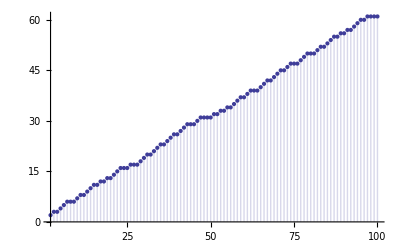

```mathematica
DiscretePlot[ Sum[ MoebiusMu[j]^2,{j,1,n}],{n,2,100}]
```

```mathematica
FH[n_, k_, s_ ]:= FH[n,k,s]=Sum[ FF[j,s]( 1/(k!)+FH[Floor[n/j], k+1, s]), {j,2,n}]
```

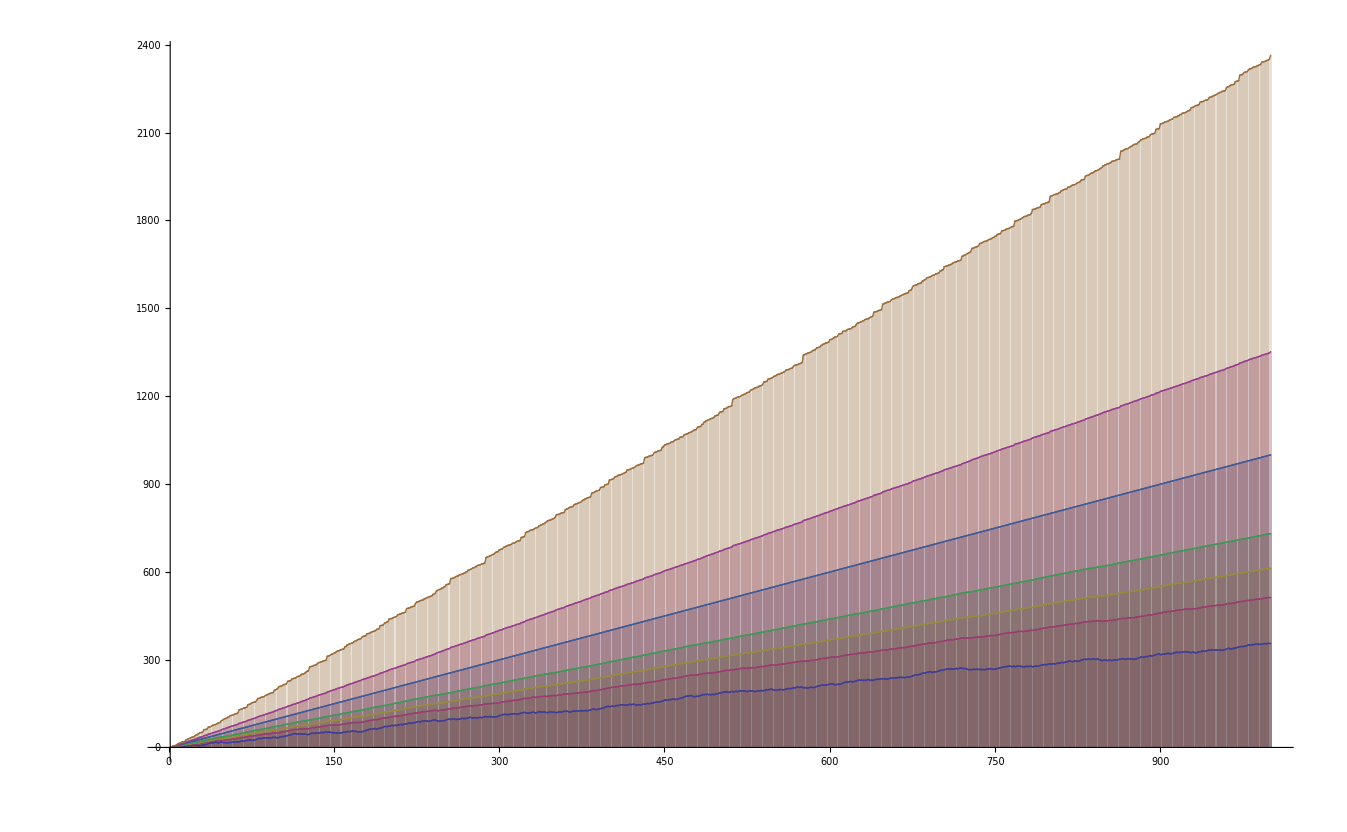

```mathematica
DiscretePlot[ {FH[n,1,-4],FH[n,1,-2],FH[n,1,-1],FH[n,1,0],FH[n,1,1],FH[n,1,2],FH[n,1,4]},{n,2,1000}, ExtentSize->Full]
```

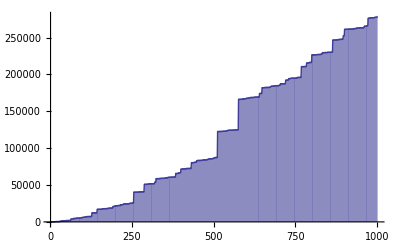

```mathematica
DiscretePlot[ {FH[n,1,40]},{n,2,1000}, ExtentSize->Full]
```